## Set notebook directory

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
(*In this document was chosen a fcuntion to work with in the next steps and it is define as f(x). Also, was defined the subinterval and its convergence according to the Gaussian Quadrature*)
Needs["NumericalDifferentialEquationAnalysis`"];
```

# Benchmark

```mathematica
p=10; (*Número de pontos*)
d=10; (*10^d Representa a precisão desejada*)
a=-10; (*Menor limite de integração*)
b=10;(*Maior limite de integração*)
e=1.0; (*espaçemtno*)
Nintegrations=10;

fontsize=20;
res=400;
```

```mathematica
c5=Table[a+i*e  -e ->  a+i*e ,{i,1,(b-a)*(1/e)}];
```

```mathematica
f[x_]=ArcTan[(x-5)^2];
```

```mathematica
ExactIntegral=Integrate[f[x],{x,a,b}]//N
```

27.2397+0. ⅈ

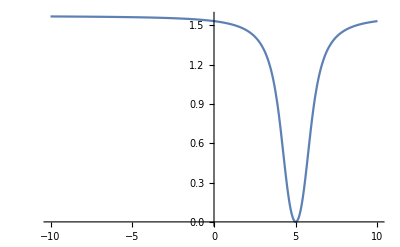

```mathematica
Plot[f[x],{x,a,b},PlotRange->All]
```

## Gauss Quadrature:

### General Method

```mathematica
Gauss[n_,a_,b_]:=Module[{aux,Wivec,fvec, valor},
(*"n" representa o número de pontos de integração*)
aux=SetPrecision[GaussianQuadratureWeights[n,a,b],MachinePrecision];
Wivec=aux[[All,2]];
fvec=f[aux[[All,1]]];
valor=fvec.Wivec;
Return[valor];
];
```

### Dividing the function:

```mathematica
(*Convergência da função f(x)*)
```

```mathematica
Chop[Table[Abs[Gauss[i,a,b]-Integrate[f[x],{x,a,b}]],{i,1,p}],10^-d]
```

{3.37666,6.22615,3.05417,1.37079,3.06606,1.95864,0.171002,1.33273,1.06556,0.0977485}

```mathematica
(*Plotagem da divisão*)
```

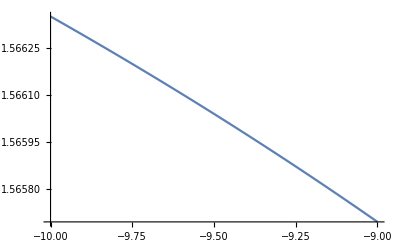
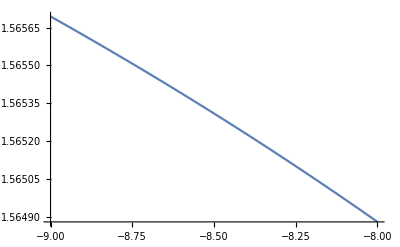
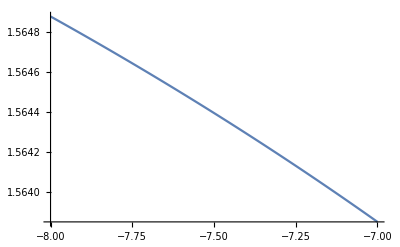
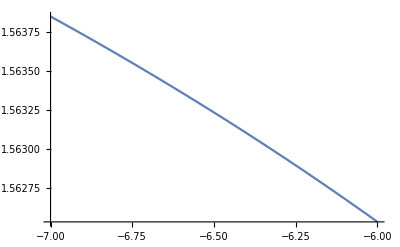
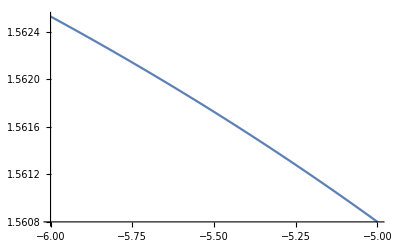
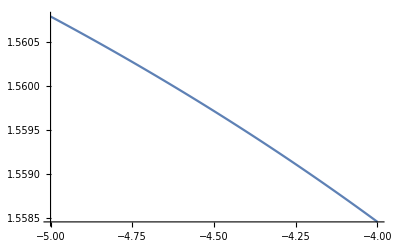
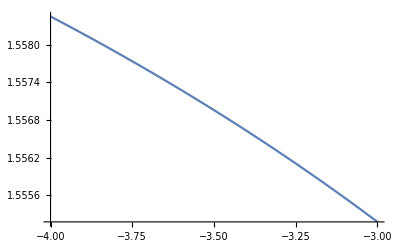
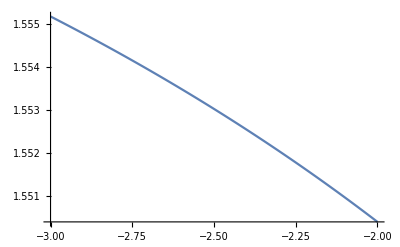

```mathematica
Table[Plot[f[x],{x,(a+i*e)-e,a+i*e}],{i,1,(b-a)*(1/e)}]
```

```mathematica
(*Convergência da integração numérica de Gauss para cada segmento da função f(x)*)
```

```mathematica
integrations=Table[Abs[Gauss[n,(a+i*e)-e,a+i*e]-NIntegrate[f[x],{x,(a+i*e)-e,a+i*e}]],{i,1,(b-a)*(1/e)},{n,1,Nintegrations}];
plotsdata=Table[integrations[[All,i]],{i,1,Nintegrations,1}];
minimumdata=Table[Flatten[Position[Chop[plotsdata[[All,i]],10^-d],0]][[1]],{i,1,Dimensions[integrations][[1]],1}];
AppendTo[plotsdata,10^-d+0integrations[[All,1]]];
plotslegends=Table[Style["n = " <> ToString[i],FontSize->fontsize],{i,1,Nintegrations,1}];
```

```mathematica
minimumdata
```

{3,3,3,3,3,3,3,4,4,4,4,5,6,8,9,9,8,6,5,4}

```mathematica
plotsdata[[All,1]]
```

{5.66189×10^-6,2.99411×10^-9,1.28009×10^-12,1.11022×10^-15,1.77636×10^-15,1.77636×10^-15,1.55431×10^-15,1.77636×10^-15,1.77636×10^-15,1.77636×10^-15,1.×10^-10}

## Rendering plots

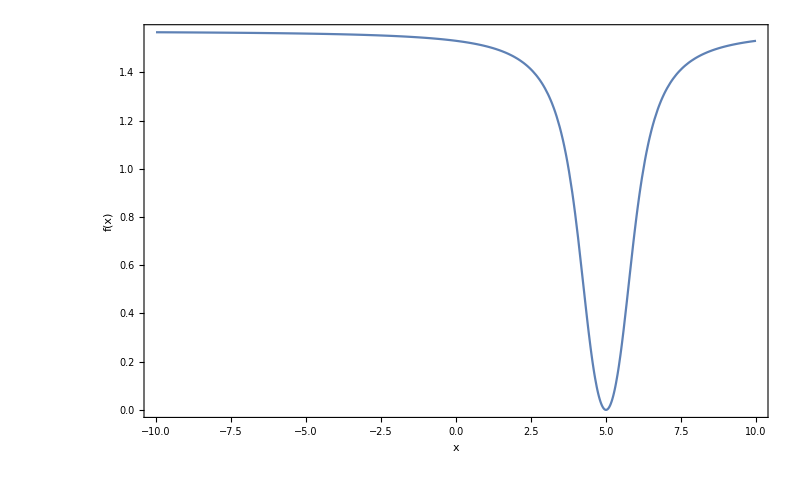

```mathematica
ComparisonPlot =ListLogPlot[plotsdata,PlotMarkers->{Automatic, Large},Joined->True,PlotLegends->plotslegends,Frame->True,FrameStyle->Directive[Black,Bold, FontSize->fontsize],FrameLabel->{ Style[" Intervalo ",FontSize->fontsize],"Abs[erro] "},ImageSize->800];
MinimumPlot =ListPlot[minimumdata,PlotMarkers->{Automatic, Large},Joined->True,Frame->True,FrameStyle->Directive[Black,Bold, FontSize->fontsize],FrameLabel->{ Style[" Intervalo ",FontSize->fontsize]," n "},ImageSize->800];
fPlot =Plot[f[x],{x,a,b},PlotRange->All,Frame->True,FrameStyle->Directive[Black,Bold, FontSize->fontsize],FrameLabel->{ Style[" x ",FontSize->fontsize]," f(x) "},ImageSize->800]
```

```mathematica
AbsoluteTiming[errorstable=Chop[TableForm[integrations,TableHeadings-> {c5,plotslegends}],10^-d]]
```

{0.000062, | n = 1 | n = 2 | n = 3 | n = 4 | n = 5 | n = 6 | n = 7 | n = 8 | n = 9 | n = 10
-10.→-9. | 5.66189×10^-6 | 2.99411×10^-9 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-9.→-8. | 7.53651×10^-6 | 4.59809×10^-9 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-8.→-7. | 0.0000102554 | 7.29871×10^-9 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-7.→-6. | 0.000014319 | 1.20412×10^-8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-6.→-5. | 0.0000206103 | 2.07923×10^-8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-5.→-4. | 0.0000307698 | 3.79238×10^-8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-4.→-3. | 0.0000480368 | 7.39582×10^-8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-3.→-2. | 0.0000793059 | 1.56814×10^-7 | 2.50404×10^-10 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-2.→-1. | 0.000140698 | 3.70196×10^-7 | 7.84965×10^-10 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1.→0 | 0.000274766 | 1.00796×10^-6 | 2.96647×10^-9 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0→1. | 0.00061367 | 3.34335×10^-6 | 1.44465×10^-8 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1.→2. | 0.00167308 | 0.0000147347 | 9.90168×10^-8 | 5.41061×10^-10 | 0 | 0 | 0 | 0 | 0 | 0
2.→3. | 0.00624341 | 0.0000953018 | 8.63041×10^-7 | 6.27736×10^-10 | 1.50674×10^-10 | 0 | 0 | 0 | 0 | 0
3.→4. | 0.0323647 | 0.0000103448 | 0.0000421858 | 1.13089×10^-7 | 7.94244×10^-8 | 2.63227×10^-10 | 1.77163×10^-10 | 0 | 0 | 0
4.→5. | 0.052924 | 0.00263421 | 0.000231908 | 0.0000164035 | 9.03097×10^-7 | 2.82661×10^-8 | 1.91198×10^-9 | 4.8872×10^-10 | 0 | 0
5.→6. | 0.052924 | 0.00263421 | 0.000231908 | 0.0000164035 | 9.03097×10^-7 | 2.82661×10^-8 | 1.91198×10^-9 | 4.8872×10^-10 | 0 | 0
6.→7. | 0.0323647 | 0.0000103448 | 0.0000421858 | 1.13089×10^-7 | 7.94244×10^-8 | 2.63227×10^-10 | 1.77163×10^-10 | 0 | 0 | 0
7.→8. | 0.00624341 | 0.0000953018 | 8.63041×10^-7 | 6.27736×10^-10 | 1.50674×10^-10 | 0 | 0 | 0 | 0 | 0
8.→9. | 0.00167308 | 0.0000147347 | 9.90168×10^-8 | 5.41061×10^-10 | 0 | 0 | 0 | 0 | 0 | 0
9.→10. | 0.00061367 | 3.34335×10^-6 | 1.44465×10^-8 | 0 | 0 | 0 | 0 | 0 | 0 | 0}

## Exporting data

```mathematica
ExportPlotsQ=True;
If[ExportPlotsQ,
Export["NpointsMethodI.png",MinimumPlot,ImageResolution->res];
Export["ErrorplotsmethodI.png",ComparisonPlot,ImageResolution->res];
Export["FunctionPlot.png",fPlot,ImageResolution->res];
];
```

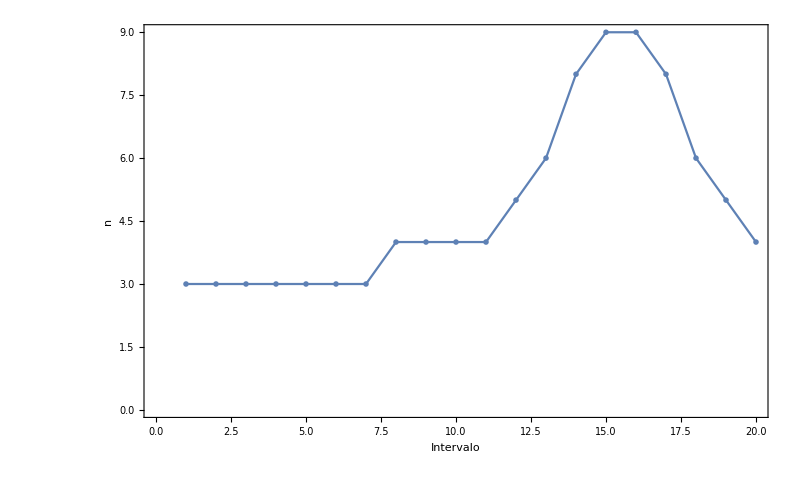

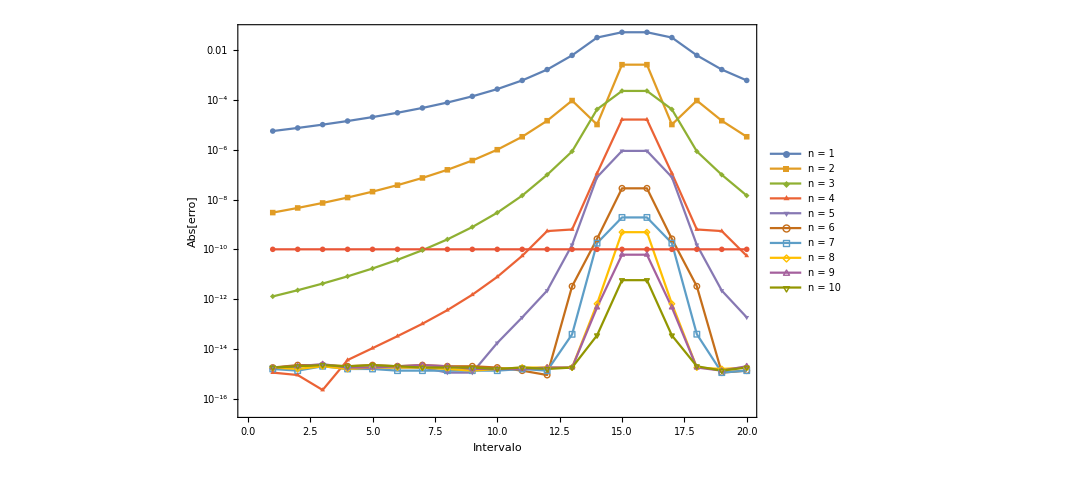

```mathematica
MinimumPlot
ComparisonPlot
```